```mathematica
ClearAll["Global`*"]
```

3-D P-C-R system
Where we examine scale and elasticities for the dimensionless version of the system (Rstar, Cstar, Pstar are dimensionless)

Scale parameters

```mathematica
scale$αr = FullSimplify[(a*Rstar*(1-Rstar))/Rstar]
scale$αc = FullSimplify[ (λC*(Rstar/(0.5+Rstar))*Cstar)/Cstar]
scale$αp = FullSimplify[(w*λP*Cstar*Pstar)/Pstar]
```

a-a Rstar

(Rstar λC)/(0.5+Rstar)

Cstar w λP

Branching Parameters

```mathematica
branching$δ = FullSimplify[1 - 1/scale$αc*(w*λP*P*C)/C/.{P->Pstar,C->Cstar}]
branching$β = FullSimplify[1/scale$αc*1/branching$δ*((μC*C)/C/.{C->Cstar})]

branching$γ = FullSimplify[1/scale$αp*((μP*P)/P/.{P->Pstar})]
```

1-(1. Pstar (0.5+Rstar) w λP)/(Rstar λC)

((0.5+Rstar) μC)/(Rstar λC-0.5 Pstar w λP-1. Pstar Rstar w λP)

μP/(Cstar w λP)

Elasticities

```mathematica
elasticity$fr=FullSimplify[(Rstar/(a*Rstar*(1-Rstar)))*((D[a*R*(1-R),R])/.R->Rstar)]
```

2+1/(-1+Rstar)

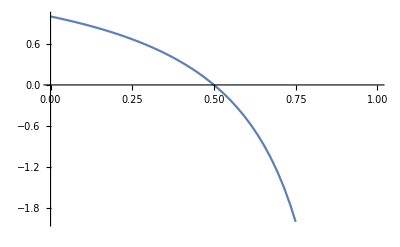

```mathematica
Plot[elasticity$fr,{Rstar,0,1},PlotRange->{-2,1}]
```

```mathematica
elasticity$gr=FullSimplify[(Rstar/(λC*(Rstar/(0.5+Rstar))*Cstar))*((D[λC*(R/(0.5+R))*C,R])/.{R->Rstar,C->Cstar})]
```

0.5/(0.5+Rstar)

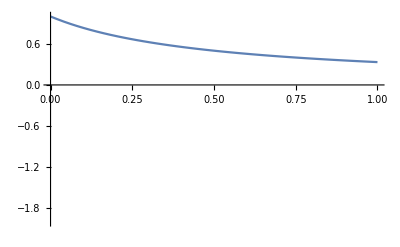

```mathematica
Plot[elasticity$gr,{Rstar,0,1},PlotRange->{-2,1}]
```

```mathematica
elasticity$gc=FullSimplify[(Cstar/(λC*(Rstar/(0.5+Rstar))*Cstar))*((D[λC*(R/(0.5+R))*C,C])/.{R->Rstar,C->Cstar})]
```

1

```mathematica
elasticity$sr=FullSimplify[(R/(σC*(1-R)*C)/.{R->Rstar,C->Cstar})*((D[σC*(1-R)*C,R])/.{R->Rstar,C->Cstar})]
```

Rstar/(-1+Rstar)

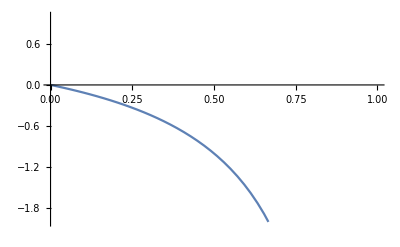

```mathematica
Plot[elasticity$sr,{Rstar,0,1},PlotRange->{-2,1}]
```

```mathematica
elasticity$sc=FullSimplify[(C/(σC*(1-R)*C)/.{R->Rstar,C->Cstar})*((D[σC*(1-R)*C,C])/.{R->Rstar,C->Cstar})]
```

1

```mathematica
elasticity$bc = FullSimplify[(C/(w*λP*P*C)/.{P->Pstar,C->Cstar})*((D[w*λP*P*C,C])/.{P->Pstar,C->Cstar})]
```

1

```mathematica
elasticity$bp = FullSimplify[(P/(w*λP*P*C)/.{P->Pstar,C->Cstar})*((D[w*λP*P*C,P])/.{P->Pstar,C->Cstar})]
```

1

```mathematica
elasticity$mc = FullSimplify[(C/(μC*C)/.{C->Cstar})*((D[μC*C,C])/.{C->Cstar})]
```

1

```mathematica
elasticity$tc = FullSimplify[(C/(σP*(1-C)*P)/.{P->Pstar,C->Cstar})*((D[σP*(1-C)*P,C])/.{P->Pstar,C->Cstar})]
```

Cstar/(-1+Cstar)

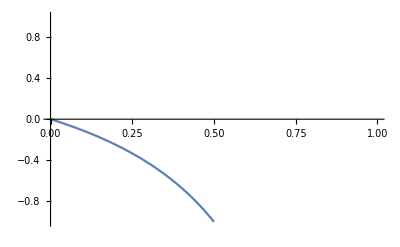

```mathematica
Plot[elasticity$tc,{Cstar,0,1},PlotRange->{-1,1}]
```

```mathematica
elasticity$tp = FullSimplify[(P/(σP*(1-C)*P)/.{P->Pstar,C->Cstar})*((D[σP*(1-C)*P,P])/.{P->Pstar,C->Cstar})]
```

1

```mathematica
elasticity$qp = FullSimplify[(P/(μP*P)/.{P->Pstar})*((D[μP*P,P])/.{P->Pstar})]
```

1

```mathematica
JacobianGeneral2D={
{ αc*(gc-δ*(β*mc+(1-β)*sc)-(1-δ)*bc),αc*(gr-δ*(1-β)*sr)},
{-αr*gc,αr*(fr-gr)}};
JacobianGeneral2D//MatrixForm
```

(αc (gc-bc (1-δ)-(sc (1-β)+mc β) δ) | αc (gr-sr (1-β) δ)
-gc αr | (fr-gr) αr)

```mathematica
JacobianGeneral3D = {
{αp*(bp-γ*qp-(1-γ)*tp),αp*(bc-(1-γ)*tc),0},
{-αc*(1-δ)*bp, αc*(gc-δ*(β*mc+(1-β)*sc)-(1-δ)*bc),αc*(gr-δ*(1-β)*sr)},
{0,-αr*gc,αr*(fr-gr)}};
JacobianGeneral3D//MatrixForm
```

(αp (bp-tp (1-γ)-qp γ) | αp (bc-tc (1-γ)) | 0
-bp αc (1-δ) | αc (gc-bc (1-δ)-(sc (1-β)+mc β) δ) | αc (gr-sr (1-β) δ)
0 | -gc αr | (fr-gr) αr)

```mathematica
JacobianSpecific2D =FullSimplify[JacobianGeneral2D/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
fr->elasticity$fr,
gr->elasticity$gr,
gc->elasticity$gc,
sr->elasticity$sr,
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp
}];
JacobianSpecific3D =FullSimplify[JacobianGeneral3D/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
fr->elasticity$fr,
gr->elasticity$gr,
gc->elasticity$gc,
sr->elasticity$sr,
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp
}];
JacobianSpecific2D//MatrixForm
JacobianSpecific3D//MatrixForm
```

(0. | -(1. Rstar ((0.5+Rstar^2) λC+(0.5+1. Rstar)^2 (-1. Pstar w λP-1. μC)))/(-0.25-0.75 Rstar+Rstar^3)
a (-1+Rstar) | -(2. a (-0.25+Rstar) Rstar)/(0.5+Rstar))

(0 | (Cstar (-w λP+μP))/(-1+Cstar) | 0
-1. Pstar w λP | 0. | -(1. Rstar ((0.5+Rstar^2) λC+(0.5+1. Rstar)^2 (-1. Pstar w λP-1. μC)))/(-0.25-0.75 Rstar+Rstar^3)
0 | a (-1+Rstar) | -(2. a (-0.25+Rstar) Rstar)/(0.5+Rstar))

Derive Stability Conditions

```mathematica
CP2D = FullSimplify[CharacteristicPolynomial[JacobianSpecific2D,L]]
```

0.+1. L^2+(a L Rstar (-0.5+2. Rstar))/(0.5+Rstar)+(a Rstar (1. (-1.+1. Rstar) (0.5+1. Rstar^2) λC+(0.25+0.75 Rstar-1. Rstar^3) (Pstar w λP+μC)))/(-0.25-0.75 Rstar+Rstar^3)

```mathematica
CP2DList = CoefficientList[CP2D,L]
```

{0.+(a Rstar (1. (-1.+1. Rstar) (0.5+1. Rstar^2) λC+(0.25+0.75 Rstar-1. Rstar^3) (Pstar w λP+μC)))/(-0.25-0.75 Rstar+Rstar^3),(a Rstar (-0.5+2. Rstar))/(0.5+Rstar),1.}

```mathematica
FullSimplify[μC/.Flatten[Solve[Det[JacobianSpecific2D]==0,μC],1]]
```

-(1. (0.+(a Rstar (-1. (-1.+1. Rstar) (0.5+1. Rstar^2) λC+Pstar (-0.25-0.75 Rstar+1. Rstar^3) w λP))/(-0.25-0.75 Rstar+Rstar^3)))/(a Rstar)

Solve Specific Model and Introduce Allometric Relationships

```mathematica
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+bP)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],bP->bP[M]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R)))*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],bP->bP[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[4]]
Rsol = R/.LVSS[[4]]
```

-1/(4 λ[M] σ[M]^2)α Y[M] (2 kRes (bP[M]-λ[M]+μ[M])^2+kRes (3 bP[M]-λ[M]+3 μ[M]) σ[M]+bP[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-λ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+μ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2)))

(kRes (2 (bP[M]-λ[M]+μ[M])+σ[M])+√(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2)))/(4 σ[M])

```mathematica
JacobianFullModel=({
{D[eqnC,C],D[eqnC,R]},
{D[eqnR,C],D[eqnR,R]}})/.{C->Csol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/ppmr_fit_table.csv"}],"csv"];
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ1=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
(*ρ[M_]:=B0*M^(η)/(M*Ed);*)
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ1+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)

(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ppmrint*M^ppmrslope;
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)



OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; 
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify]; 
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*predatedconsumerdensity[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];

bP[M_] :=predmortalityfull[OptPredMass[M],M];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

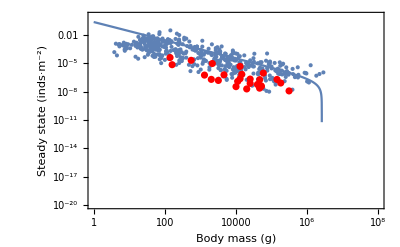

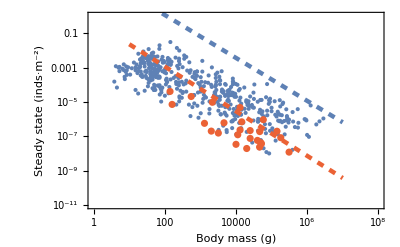

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-20,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"}],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.bP[M]->0,{M,1,10^7},Frame->True,PlotStyle->ColorData[97,1]]
}]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M],{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/M)*PredatorDensityTheoreticalMax[OptPredMass[M],M],{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

Now repopulate the 2D Jacobian with the allometric relationships

```mathematica
JacobianSpecific2D//MatrixForm
```

(0. | -(1. Rstar ((0.5+Rstar^2) λC+(0.5+1. Rstar)^2 (-1. Pstar w λP-1. μC)))/(-0.25-0.75 Rstar+Rstar^3)
8.13994×10^-6 (-1+Rstar) | -(0.0000162799 (-0.25+Rstar) Rstar)/(0.5+Rstar))

```mathematica
JacobianAllometric2D =JacobianSpecific2D/.{
Rstar -> Rsol/kRes,
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
μC->μ[M]
};
```

```mathematica
Eig = Eigenvalues[(JacobianAllometric2D/.M->10^(6.9))];
RealEig = Re[Eig]
ImEig = Im[Eig]
```

{-8.75987×10^-6,3.5497×10^-9}

{0,0}

```mathematica
Manipulate[
Eig = Eigenvalues[(JacobianAllometric2D/.M->(10^i))];
RealEig = Re[Eig];
ImEig = Im[Eig];
ListPlot[Transpose[{RealEig,ImEig}],PlotRange->{{-1,1},{-1,1}},PlotLabel->Max[RealEig]],
{i,0,8}]
```

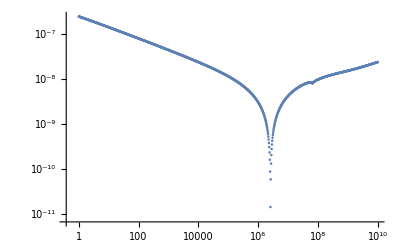

```mathematica
ListLogLogPlot[
EigTable=Table[
Eig = Eigenvalues[(JacobianAllometric2D/.M->(10^i))];
RealEig = Re[Eig];
{10^i,Abs[Max[RealEig]]},
{i,0,10,0.01}]
]
```

```mathematica
EigTable[[Flatten[Position[EigTable[[All,2]],Min[EigTable[[All,2]]]],1][[1]]]]
```

{2.5704×10^6,1.43419×10^-11}

Compare the scaled model above to the full model

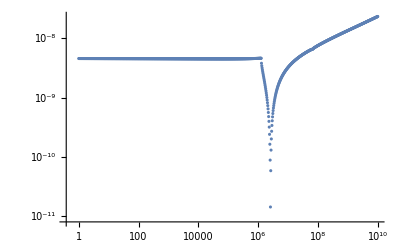

```mathematica
ListLogLogPlot[
EigTableFull=Table[
EigFull = Eigenvalues[(JacobianFullModel/.M->(10^i))];
RealEigFull = Re[EigFull];
{10^i,Abs[Max[RealEigFull]]},
{i,0,10,0.01}]
]
```

```mathematica
EigTable[[Flatten[Position[EigTableFull[[All,2]],Min[EigTableFull[[All,2]]]],1][[1]]]]
```

{2.5704×10^6,1.43419×10^-11}

How to important scale, branching, and elasticity parameters change with Consumer Mass?
alphac
alphar
fr
gr
delta
beta
sr

```mathematica
allo$αc = scale$αc/.{Rstar -> Rsol/kRes,Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),w->1,λC->λ[M],λP->λPred[OptPredMass[M]],μC->μ[M]};
allo$αr = scale$αr/.{Rstar -> Rsol/kRes,Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),w->1,λC->λ[M],λP->λPred[OptPredMass[M]],μC->μ[M]};
allo$β= branching$β/.{Rstar -> Rsol/kRes,Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),w->1,λC->λ[M],λP->λPred[OptPredMass[M]],μC->μ[M]};
allo$δ = branching$δ/.{Rstar -> Rsol/kRes,Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),w->1,λC->λ[M],λP->λPred[OptPredMass[M]],μC->μ[M]};
allo$fr = elasticity$fr/.{Rstar -> Rsol/kRes,Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),w->1,λC->λ[M],λP->λPred[OptPredMass[M]],μC->μ[M]};
allo$gr = elasticity$gr/.{Rstar -> Rsol/kRes,Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),w->1,λC->λ[M],λP->λPred[OptPredMass[M]],μC->μ[M]};
allo$sr = elasticity$sr/.{Rstar -> Rsol/kRes,Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),w->1,λC->λ[M],λP->λPred[OptPredMass[M]],μC->μ[M]};
```

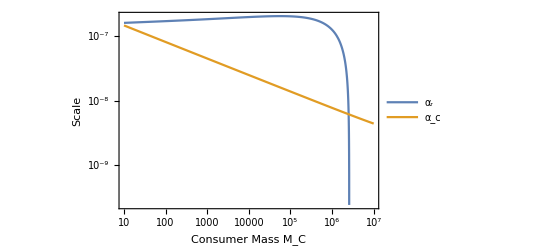

```mathematica
LogLogPlot[{allo$αr,allo$αc},{M,10^1,10^7},Frame->True,PlotLegends->{"α_r","α_c"},FrameLabel->{"Consumer Mass M_C","Scale"}]
```

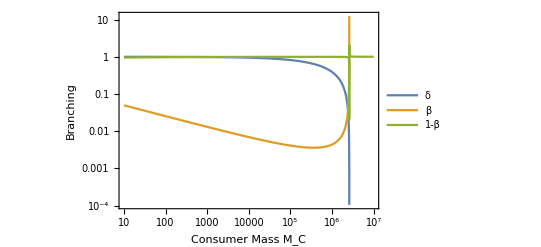

```mathematica
LogLogPlot[{
allo$δ,
allo$β,
1-allo$β},{M,10^1,10^7},Frame->True,PlotLegends->{"δ","β","1-β"},FrameLabel->{"Consumer Mass M_C","Branching"}]
```

What are the bifurcation conditions for the Generalized Model?
Relate the scale

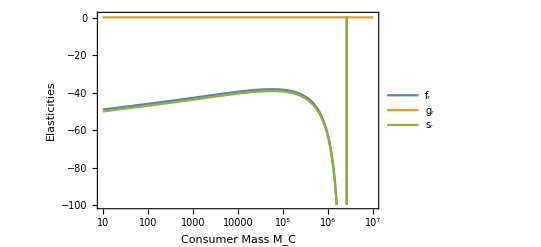

```mathematica
LogLinearPlot[{allo$fr ,allo$gr,allo$sr},{M,10^1,10^7},Frame->True,PlotLegends->{"f_r","g_r","s_r"},FrameLabel->{"Consumer Mass M_C","Elasticities"},PlotRange->{-100,1}]
```

```mathematica
allo$gr/.M->10000
```

0.338784

```mathematica
0.5/(1.5)
```

0.333333

```mathematica
TransCritBifApprox = FullSimplify[Solve[Det[(JacobianGeneral2D/.{gr->(1/3),sr->fr})]==0,fr]]
```

{{fr→(-bc+(bc+sc (-1+β)-mc β) δ)/(3 (-bc+gc+(bc+gc (-1+β)+sc (-1+β)-mc β) δ))}}

```mathematica
HopfBifApprox =  FullSimplify[Solve[Tr[(JacobianGeneral2D/.{gr->(1/3),sr->fr})]==0,fr]]
```

{{fr→1/3+(αc (bc-gc-bc δ+(sc+mc β-sc β) δ))/αr}}

Recall in the specific model:
gc = sc = bc = bp = mc = tp = qp = 1

```mathematica
TransCritBifApprox=TransCritBifApprox/.{gc->1,sc->1,bc->1,bp->1,mc->1,tp->1,qp->1}
HopfBifApprox = HopfBifApprox/.{gc->1,sc->1,bc->1,bp->1,mc->1,tp->1,qp->1}
```

{{fr→-1/(3 (-1+β) δ)}}

{{fr→1/3}}

```mathematica
Plot3D[fr/.TransCritBifApprox,{δ,0,1},{β,0,1},PlotRange->{-50,50},BoundaryStyle->None,AxesLabel->{"δ","β","fr"}]
```

-Graphics3D-

```mathematica
MassTrajectory=ParallelTable[Re[({branching$δ,branching$β,elasticity$fr}/.{
Rstar -> Rsol/kRes,
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
μC->μ[M]})/.M->10^i],{i,0,8,0.01}];
```

```mathematica
Show[{
Plot3D[fr/.TransCritBifApprox,{δ,0,1},{β,-1,1},PlotRange->{-100,5},BoundaryStyle->None,AxesLabel->{"δ","β","fr"}],
Plot3D[fr/.HopfBifApprox,{δ,0,1},{β,-1,1}],
ListPointPlot3D[MassTrajectory]
}]
```

-Graphics3D-

```mathematica
TransCritBifSpecific = NSolve[Det[JacobianAllometric2D]==0,M]
```

$Aborted

```mathematica
TransCritBifSpecific =FullSimplify[β/. TransCritBifGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
fr->elasticity$fr,
gr->elasticity$gr,
gc->elasticity$gc,
sr->elasticity$sr,
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp
}];
```

```mathematica
TransCritBifSpecific
```

{1+((0.333333-0.333333 Rstar) λC)/(1. Rstar λC-0.5 Pstar w λP-1. Pstar Rstar w λP)}

```mathematica
BT=Table[
{10^i,w,(TransCritBifSpecific/.{
Rstar -> Rsol/kRes,
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
μC->μ[M]
})/.M->10^i},{i,1,7,0.5},{w,0,2,0.1}]
```